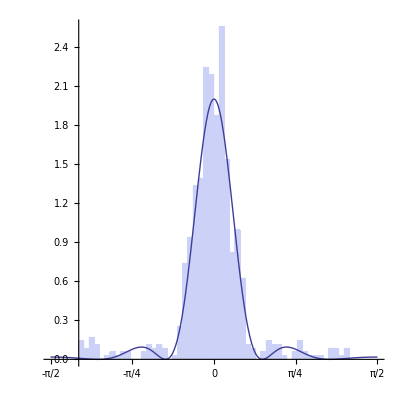
-Graphics-10

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/BohmianSingleSlitHist3.dat"]];
Labeled[Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14},Ticks->{{-π/2,-π/4,0,π/4,π/2},Automatic}],Plot[{2.0(Sinc[7 Sin[x]]^2)},{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}],ToString[10],{{Right,Top}}]
```